# Fits to Brody distribution, and calculations for density of states

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

### Run 0

```mathematica
(*rundata0=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/4BodySVD.par","text"]*)
rundata0=Import["./4BodySVD.par","text"]
SampleRange=Ecutoff0-30.0<#<Ecutoff0-1.0&
curvestemp0=Transpose[Import["./AdiabaticCurves.dat"]];
Curves0=Table[Table[{curvestemp0[[1,i]],curvestemp0[[j,i]]},{i,1,Length[curvestemp0[[1]]]}],{j,2,Length[curvestemp0]}];
Evals0=Flatten[Import["./Eigenvals.dat"]];
Ecutoff0=Evals0[[4]]
Evals0=Sort[Drop[Evals0,1;;4]];
eValsBound0 = Sort[Select[Evals0,SampleRange]];
```

xPoints (phi)		yPoints (theta)
20			20

LobattoPoints		NumChannels	Order
64			20		5

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
20.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

Ecutoff0-30.<#1<Ecutoff0-1.&

-43.1067

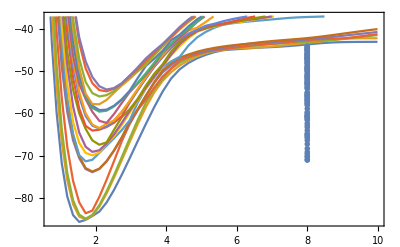

```mathematica
pcurves0=ListPlot[Curves0,Frame->True,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp0[[2]]],Ecutoff0+6}];
penergies0=ListPlot[Table[{8,eValsBound0[[i]]},{i,1,Length[eValsBound0]}],Frame->True,PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{0,0},{5,0}}]}]];
Show[pcurves0,penergies0,PlotRange->Automatic]
```

```mathematica
Es0=Table[eValsBound0[[i+1]]-eValsBound0[[i]],{i,1,Length[eValsBound0]-1}];
eTrim0 = Select[Es0,#>0.0000001&];
avg0 = Mean[eTrim0];
eTrim0 = eTrim0/avg0;
(*Sort[eTrim0];*)
Length[Es0];
Length[eTrim0];
ρ0=1/avg0;
EspaceBin0=BinCounts[eTrim0,{bins}];
NormBrodyBinCs0=Table[EspaceBin0[[i]]/Total[EspaceBin0]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist0 = Table[{bFit[[i]],NormBrodyBinCs0[[i]]},{i,1,Length[bFit]}]
phist0=ListPlot[brodyPdist0,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars0 = FindFit[brodyPdist0,{PBrody[s,w],w>0,w<1},{w},s]
pfit0=Plot[PBrody[s,w/.pars0],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.196078},{0.3,0.539216},{0.5,0.931373},{0.7,1.32353},{0.9,0.392157},{1.1,0.490196},{1.3,0.196078},{1.5,0.147059},{1.7,0.0980392},{1.9,0.0490196},{2.1,0.0980392},{2.3,0.0980392},{2.5,0.},{2.7,0.0490196},{2.9,0.0980392},{3.1,0.147059},{3.3,0.0980392},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.0490196},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.621668}

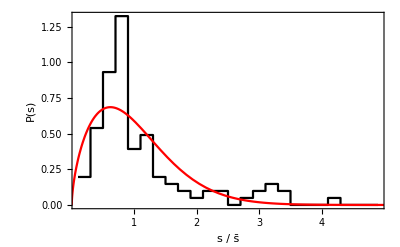

```mathematica
Show[phist0,pfit0,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run1

```mathematica
rundata1=Import["./run1/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			80

LobattoPoints		NumChannels	Order
80			60		5

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
40.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff1-30.0<#<Ecutoff1-1.0&
curvestemp1=Transpose[Import["./run1/AdiabaticCurves.dat"]];
Curves1=Table[Table[{curvestemp1[[1,i]],curvestemp1[[j,i]]},{i,1,Length[curvestemp1[[1]]]}],{j,2,Length[curvestemp1]}];
Evals1=Flatten[Import["./run1/Eigenvals.dat"]];
Ecutoff1=Evals1[[4]]
Evals1=Sort[Drop[Evals1,1;;4]];
eValsBound1 = Sort[Select[Evals1,SampleRange]]
```

Ecutoff1-30.<#1<Ecutoff1-1.&

-92.4746

{-121.61,-121.216,-120.765,-120.5,-119.99,-117.553,-117.246,-117.119,-116.484,-115.777,-115.681,-114.184,-113.676,-113.449,-113.215,-112.903,-111.217,-110.946,-110.368,-110.101,-110.013,-109.749,-109.055,-108.859,-107.45,-107.042,-107.023,-106.687,-106.435,-106.232,-105.279,-104.82,-104.127,-104.018,-103.859,-103.543,-103.394,-102.56,-102.16,-102.088,-101.971,-101.603,-101.375,-100.702,-100.209,-100.181,-99.9099,-99.4771,-99.2265,-98.503,-98.3685,-98.0915,-97.847,-97.7527,-97.4852,-96.9485,-96.6677,-96.303,-96.228,-96.0919,-95.8766,-95.4007,-95.159,-94.8188,-94.5748,-94.2611,-94.0011,-93.9079,-93.8485,-93.7073}

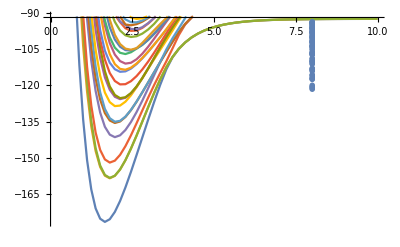

```mathematica
pcurves1=ListPlot[Curves1,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp1[[2]]],Ecutoff1+1}];
penergies1=ListPlot[Table[{8,eValsBound1[[i]]},{i,1,Length[eValsBound1]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves1,penergies1]
```

```mathematica
Es1=Table[eValsBound1[[i+1]]-eValsBound1[[i]],{i,1,Length[eValsBound1]-1}];
eTrim1= Select[Es1,#>0.0000001&];
avg1 = Mean[eTrim1];
eTrim1 = eTrim1/avg1;
(*Sort[eTrim1];*)
Length[Es1];
Length[eTrim1];
ρ1=1/avg1;
EspaceBin1=BinCounts[eTrim1,{bins}];
NormBrodyBinCs1=Table[EspaceBin1[[i]]/Total[EspaceBin1]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist1 = Table[{bFit[[i]],NormBrodyBinCs1[[i]]},{i,1,Length[bFit]}]
phist1=ListPlot[brodyPdist1,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars1 = FindFit[brodyPdist1,{PBrody[s,w],w>0,w<1},{w},s]
pfit1=Plot[PBrody[s,w/.pars1],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.367647},{0.3,0.882353},{0.5,0.514706},{0.7,1.25},{0.9,0.441176},{1.1,0.367647},{1.3,0.294118},{1.5,0.147059},{1.7,0.367647},{1.9,0.},{2.1,0.0735294},{2.3,0.0735294},{2.5,0.},{2.7,0.},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.0735294},{3.7,0.0735294},{3.9,0.},{4.1,0.0735294},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.440578}

```mathematica
ρ1
```

2.47285

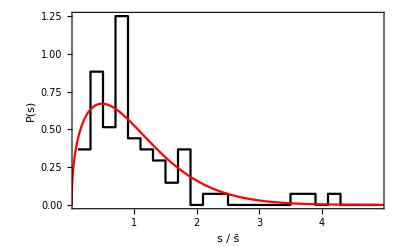

```mathematica
Show[phist1,pfit1,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run2

```mathematica
rundata2=Import["./run2/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			80

LobattoPoints		NumChannels	Order
80			60		5

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
40.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		1		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff2-30.0<#<Ecutoff2-1&
curvestemp2=Transpose[Import["./run2/AdiabaticCurves.dat"]];
Curves2=Table[Table[{curvestemp2[[1,i]],curvestemp2[[j,i]]},{i,1,Length[curvestemp2[[1]]]}],{j,2,Length[curvestemp2]}];
Evals2=Flatten[Import["./run2/Eigenvals.dat"]];
Ecutoff2=Evals2[[4]]
Evals2=Sort[Drop[Evals2,1;;4]];
eValsBound2 = Sort[Select[Evals2,SampleRange]]
```

Ecutoff2-30.<#1<Ecutoff2-1&

-92.4746

{-122.413,-121.312,-120.73,-120.439,-118.683,-117.761,-117.45,-117.288,-117.048,-116.962,-116.542,-116.306,-115.805,-115.616,-115.541,-115.17,-113.967,-113.265,-112.881,-111.855,-110.973,-110.58,-110.215,-110.099,-109.866,-109.703,-109.61,-109.134,-108.734,-108.663,-108.308,-107.528,-107.188,-106.715,-106.577,-106.345,-105.85,-105.486,-105.296,-104.848,-104.333,-104.104,-103.972,-103.621,-103.533,-103.508,-103.394,-102.647,-102.633,-102.13,-101.855,-101.502,-101.13,-100.823,-100.347,-99.9502,-99.8741,-99.7306,-99.6587,-99.3396,-99.163,-98.9668,-98.7859,-98.1867,-97.8806,-97.7346,-97.6702,-97.3509,-97.2891,-96.6696,-96.468,-96.2869,-96.0941,-96.0594,-95.9964,-95.9252,-95.8154,-95.2423,-95.086,-94.7746,-94.6698,-94.3021,-93.8984,-93.8347,-93.7949,-93.6751}

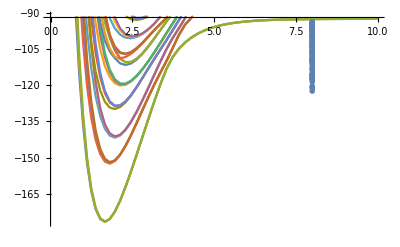

```mathematica
pcurves2=ListPlot[Curves2,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp2[[2]]],Ecutoff2+1}];
penergies2=ListPlot[Table[{8,eValsBound2[[i]]},{i,1,Length[eValsBound2]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves2,penergies2]
```

```mathematica
Es2=Table[eValsBound2[[i+1]]-eValsBound2[[i]],{i,1,Length[eValsBound2]-1}];
eTrim2 = Select[Es2,#>0.0000001&];
avg2 = Mean[eTrim2];
eTrim2 = eTrim2/avg2;
(*Sort[eTrim2];*)
Length[Es2];
Length[eTrim2];
ρ2=1/avg2;
EspaceBin2=BinCounts[eTrim2,{bins}];
NormBrodyBinCs2=Table[EspaceBin2[[i]]/Total[EspaceBin2]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist2 = Table[{bFit[[i]],NormBrodyBinCs2[[i]]},{i,1,Length[bFit]}]
phist2=ListPlot[brodyPdist2,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars2 = FindFit[brodyPdist2,{PBrody[s,w],w>0,w<1},{w},s]
pfit2=Plot[PBrody[s,w/.pars2],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.47619},{0.3,0.833333},{0.5,0.833333},{0.7,0.297619},{0.9,0.47619},{1.1,0.833333},{1.3,0.178571},{1.5,0.357143},{1.7,0.178571},{1.9,0.0595238},{2.1,0.0595238},{2.3,0.119048},{2.5,0.},{2.7,0.119048},{2.9,0.},{3.1,0.0595238},{3.3,0.0595238},{3.5,0.0595238},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.319464}

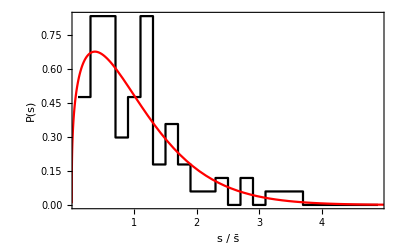

```mathematica
Show[phist2,pfit2,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run3

```mathematica
rundata3=Import["./run3/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
80			80

LobattoPoints		NumChannels	Order
80			120		5

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
40.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff3-30.0<#<Ecutoff3-1&
curvestemp3=Transpose[Import["./run3/AdiabaticCurves.dat"]];
Curves3=Table[Table[{curvestemp3[[1,i]],curvestemp3[[j,i]]},{i,1,Length[curvestemp3[[1]]]}],{j,2,Length[curvestemp3]}];
Evals3=Flatten[Import["./run3/Eigenvals.dat"]];
Ecutoff3=Evals3[[4]]
Evals3=Sort[Drop[Evals3,1;;4]];
eValsBound3 = Sort[Select[Evals3,SampleRange]]
```

Ecutoff3-30.<#1<Ecutoff3-1&

-92.4746

{-122.413,-121.61,-121.312,-121.216,-120.765,-120.73,-120.5,-120.439,-119.99,-118.683,-117.761,-117.553,-117.45,-117.288,-117.246,-117.119,-117.048,-116.962,-116.542,-116.484,-116.306,-115.805,-115.777,-115.681,-115.616,-115.541,-115.17,-114.184,-113.967,-113.676,-113.449,-113.265,-113.215,-112.903,-112.881,-111.855,-111.217,-110.973,-110.946,-110.58,-110.368,-110.215,-110.101,-110.099,-110.013,-109.866,-109.749,-109.703,-109.61,-109.134,-109.055,-108.859,-108.734,-108.663,-108.308,-107.528,-107.45,-107.188,-107.042,-107.023,-106.715,-106.687,-106.577,-106.435,-106.345,-106.232,-105.85,-105.486,-105.296,-105.279,-104.848,-104.82,-104.333,-104.127,-104.104,-104.018,-103.972,-103.859,-103.621,-103.542,-103.533,-103.508,-103.394,-103.394,-102.647,-102.633,-102.56,-102.16,-102.13,-102.088,-101.971,-101.855,-101.603,-101.502,-101.375,-101.13,-100.824,-100.702,-100.347,-100.209,-100.181,-99.9503,-99.9098,-99.8742,-99.7306,-99.6588,-99.477,-99.3396,-99.2264,-99.163,-98.9669,-98.7859,-98.5029,-98.3684,-98.1868,-98.0915,-97.8808,-97.8469,-97.7526,-97.7347,-97.6703,-97.4851,-97.3511,-97.2893,-96.9484,-96.6696,-96.6676,-96.4681,-96.3029,-96.2871,-96.228,-96.0941,-96.0919,-96.0595,-95.9965,-95.9252,-95.8765,-95.8154,-95.4007,-95.2424,-95.1589,-95.0861,-94.8187,-94.7746,-94.67,-94.5748,-94.3022,-94.261,-94.0011,-93.9078,-93.8984,-93.8484,-93.8348,-93.795,-93.7072,-93.6752}

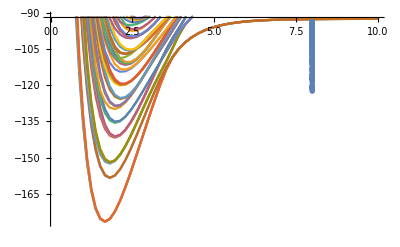

```mathematica
pcurves3=ListPlot[Curves3,Joined->True,PlotRange->{Min[curvestemp3[[2]]],Ecutoff3+1}];
penergies3=ListPlot[Table[{8,eValsBound3[[i]]},{i,1,Length[eValsBound3]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves3,penergies3]
```

```mathematica
Es3=Table[eValsBound3[[i+1]]-eValsBound3[[i]],{i,1,Length[eValsBound3]-1}];
eTrim3 = Select[Es3,#>0.0000001&];
avg3 = Mean[eTrim3];
eTrim3 = eTrim3/avg3;
Sort[eTrim3];
Length[Es3];
Length[eTrim3];
ρ3=1/avg3;
EspaceBin3=BinCounts[eTrim3,{bins}];
NormBrodyBinCs3=Table[EspaceBin3[[i]]/Total[EspaceBin3]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist3 = Table[{bFit[[i]],NormBrodyBinCs3[[i]]},{i,1,Length[bFit]}]
phist3=ListPlot[brodyPdist3,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars3 = FindFit[brodyPdist3,{PBrody[s,w],w>0,w<1},{w},s]
pfit3=Plot[PBrody[s,w/.pars3],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.855263},{0.3,0.855263},{0.5,0.690789},{0.7,0.690789},{0.9,0.328947},{1.1,0.296053},{1.3,0.230263},{1.5,0.230263},{1.7,0.131579},{1.9,0.164474},{2.1,0.0986842},{2.3,0.0986842},{2.5,0.0986842},{2.7,0.0657895},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.0328947},{3.7,0.},{3.9,0.},{4.1,0.0328947},{4.3,0.0657895},{4.5,0.},{4.7,0.},{4.9,0.0328947}}

{w→0.0351951}

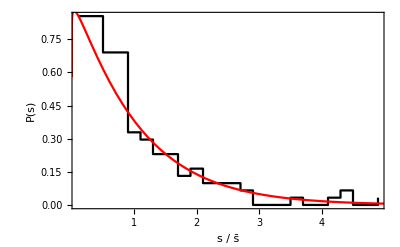

```mathematica
pall3=Show[phist3,pfit3,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

##### Analysis so far

Runs 1 and 2 have taken advantage of a possible symmetry by further reducing the coordinate space.  If my guess is right, then the density of states for run3 should be roughly twice that of run 1 and 2 since I expect both “even and odd” states about phi = π/4 to be present in run 3, but only even states in run1 and odd states in run2

```mathematica
ρ1
ρ2
ρ3
```

2.47285

2.95776

5.39359

```mathematica
ρ1+ρ2
```

5.43061

Further, I expect that if these states (even and odd) do not couple since the Hamiltonian is symmetric about ϕ=π/4, then overlaying these two distributions will result in a distribution similar to that of run3

```mathematica
eValsBoundCombined =Sort[ Flatten[{eValsBound1,eValsBound2}]]
EsCombined=Table[eValsBoundCombined[[i+1]]-eValsBoundCombined[[i]],{i,1,Length[eValsBoundCombined]-1}];
eTrimCombined = Select[EsCombined,#>0.0000001&];
avgCombined = Mean[eTrimCombined];
eTrimCombined = eTrimCombined/avgCombined;
(*Sort[eTrimCombined];*)
Length[eTrimCombined];
ρCombined=1/avgCombined;
EspaceBinCombined=BinCounts[eTrimCombined,{bins}];
NormBrodyBinCsCombined=Table[EspaceBinCombined[[i]]/Total[EspaceBinCombined]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdistCombined = Table[{bFit[[i]],NormBrodyBinCsCombined[[i]]},{i,1,Length[bFit]}]
phistCombined=ListPlot[brodyPdistCombined,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}];
parsCombined = FindFit[brodyPdistCombined,{PBrody[s,w],w>0,w<1},{w},s]
pfitCombined=Plot[PBrody[s,w/.parsCombined],{s,0,5},PlotRange->All,PlotStyle->{Red,Dashed}];
```

{-122.413,-121.61,-121.312,-121.216,-120.765,-120.73,-120.5,-120.439,-119.99,-118.683,-117.761,-117.553,-117.45,-117.288,-117.246,-117.119,-117.048,-116.962,-116.542,-116.484,-116.306,-115.805,-115.777,-115.681,-115.616,-115.541,-115.17,-114.184,-113.967,-113.676,-113.449,-113.265,-113.215,-112.903,-112.881,-111.855,-111.217,-110.973,-110.946,-110.58,-110.368,-110.215,-110.101,-110.099,-110.013,-109.866,-109.749,-109.703,-109.61,-109.134,-109.055,-108.859,-108.734,-108.663,-108.308,-107.528,-107.45,-107.188,-107.042,-107.023,-106.715,-106.687,-106.577,-106.435,-106.345,-106.232,-105.85,-105.486,-105.296,-105.279,-104.848,-104.82,-104.333,-104.127,-104.104,-104.018,-103.972,-103.859,-103.621,-103.543,-103.533,-103.508,-103.394,-103.394,-102.647,-102.633,-102.56,-102.16,-102.13,-102.088,-101.971,-101.855,-101.603,-101.502,-101.375,-101.13,-100.823,-100.702,-100.347,-100.209,-100.181,-99.9502,-99.9099,-99.8741,-99.7306,-99.6587,-99.4771,-99.3396,-99.2265,-99.163,-98.9668,-98.7859,-98.503,-98.3685,-98.1867,-98.0915,-97.8806,-97.847,-97.7527,-97.7346,-97.6702,-97.4852,-97.3509,-97.2891,-96.9485,-96.6696,-96.6677,-96.468,-96.303,-96.2869,-96.228,-96.0941,-96.0919,-96.0594,-95.9964,-95.9252,-95.8766,-95.8154,-95.4007,-95.2423,-95.159,-95.086,-94.8188,-94.7746,-94.6698,-94.5748,-94.3021,-94.2611,-94.0011,-93.9079,-93.8984,-93.8485,-93.8347,-93.7949,-93.7073,-93.6751}

{{0.1,0.855263},{0.3,0.855263},{0.5,0.690789},{0.7,0.690789},{0.9,0.328947},{1.1,0.296053},{1.3,0.230263},{1.5,0.230263},{1.7,0.131579},{1.9,0.164474},{2.1,0.0986842},{2.3,0.0986842},{2.5,0.0986842},{2.7,0.0657895},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.0328947},{3.7,0.},{3.9,0.},{4.1,0.0328947},{4.3,0.0657895},{4.5,0.},{4.7,0.},{4.9,0.0328947}}

{w→0.0351951}

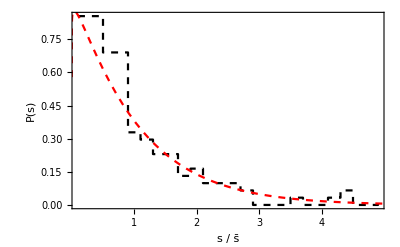

```mathematica
pcomb=Show[phistCombined,pfitCombined,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

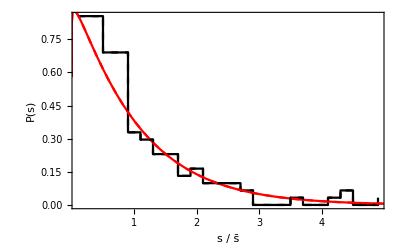

```mathematica
Show[pall3,pcomb]
```

## Run4

```mathematica
rundata4=Import["./run4/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
80			80

LobattoPoints		NumChannels	Order
80			120		5

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
40.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff4-30.0<#<Ecutoff4-1&
curvestemp4=Transpose[Import["./run4/AdiabaticCurves.dat"]];
Curves4=Table[Table[{curvestemp4[[1,i]],curvestemp4[[j,i]]},{i,1,Length[curvestemp4[[1]]]}],{j,2,Length[curvestemp4]}];
Evals4=Flatten[Import["./run4/Eigenvals.dat"]];
Ecutoff4=Evals4[[4]]
Evals4=Sort[Drop[Evals4,1;;4]];
eValsBound4 = Sort[Select[Evals4,SampleRange]]
```

Ecutoff4-30.<#1<Ecutoff4-1&

-94.3976

{-123.638,-123.48,-123.229,-122.899,-122.578,-122.549,-122.369,-122.266,-121.789,-121.28,-121.042,-121.007,-120.872,-120.688,-120.514,-120.346,-120.198,-120.062,-119.802,-119.732,-119.543,-119.302,-118.449,-118.206,-117.73,-117.598,-117.482,-117.101,-116.852,-116.81,-116.647,-116.492,-116.453,-116.388,-116.148,-115.903,-115.78,-115.537,-115.276,-114.848,-114.796,-114.547,-114.482,-114.252,-114.072,-114.057,-113.936,-113.839,-113.811,-113.543,-113.436,-113.159,-112.729,-112.705,-112.668,-112.26,-112.006,-111.755,-111.477,-111.279,-111.06,-111.002,-110.959,-110.881,-110.665,-110.624,-110.549,-110.312,-110.194,-110.144,-109.673,-109.458,-109.343,-109.233,-109.012,-108.87,-108.583,-108.398,-108.28,-108.19,-108.146,-107.992,-107.95,-107.898,-107.833,-107.624,-107.492,-107.41,-107.254,-106.805,-106.716,-106.663,-106.605,-106.393,-106.133,-106.058,-105.973,-105.847,-105.592,-105.504,-105.433,-105.254,-105.07,-104.944,-104.799,-104.693,-104.633,-104.486,-104.208,-104.035,-103.962,-103.824,-103.707,-103.505,-103.436,-103.36,-103.242,-103.01,-102.837,-102.777,-102.725,-102.514,-102.477,-102.286,-102.181,-102.128,-102.063,-102.02,-101.853,-101.74,-101.604,-101.52,-101.336,-101.236,-101.049,-100.98,-100.897,-100.879,-100.83,-100.551,-100.437,-100.333,-100.204,-100.183,-100.085,-100.042,-99.922,-99.8652,-99.6221,-99.5518,-99.405,-99.3821,-99.1977,-99.1732,-99.0879,-98.9708,-98.8371,-98.7437,-98.6869,-98.5659,-98.5376,-98.3813,-98.3069,-98.1639,-97.9102,-97.8561,-97.6846,-97.6201,-97.5532,-97.4508,-97.4275,-97.2456,-97.1567,-97.0122,-96.9448,-96.7839,-96.773,-96.7361,-96.7228,-96.6103,-96.5536,-96.5274,-96.3428,-96.3304,-96.2829,-96.2292,-96.0797,-96.0137,-95.8858,-95.7356,-95.6562,-95.6285,-95.5083,-95.4148}

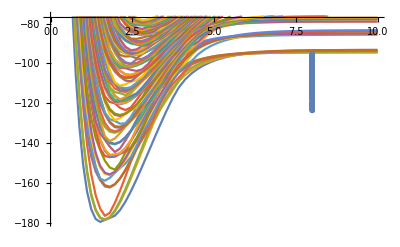

```mathematica
pcurves4=ListPlot[Curves4,Joined->True,PlotRange->{Min[curvestemp4[[2]]],Ecutoff4+18}];
penergies4=ListPlot[Table[{8,eValsBound4[[i]]},{i,1,Length[eValsBound4]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves4,penergies4]
```

```mathematica
Es4=Table[eValsBound4[[i+1]]-eValsBound4[[i]],{i,1,Length[eValsBound4]-1}];
eTrim4 = Select[Es4,#>0.0000001&];
avg4 = Mean[eTrim4];
eTrim4 = eTrim4/avg4;
Sort[eTrim4];
Length[Es4];
Length[eTrim4];
ρ4=1/avg4;
EspaceBin4=BinCounts[eTrim4,{bins}];
NormBrodyBinCs4=Table[EspaceBin4[[i]]/Total[EspaceBin4]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist4 = Table[{bFit[[i]],NormBrodyBinCs4[[i]]},{i,1,Length[bFit]}]
phist4=ListPlot[brodyPdist4,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars4 = FindFit[brodyPdist4,{PBrody[s,w],w>0,w<1},{w},s]
pfit4=Plot[PBrody[s,w/.pars4],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.390625},{0.3,0.703125},{0.5,0.729167},{0.7,0.546875},{0.9,0.625},{1.1,0.46875},{1.3,0.390625},{1.5,0.234375},{1.7,0.46875},{1.9,0.15625},{2.1,0.0260417},{2.3,0.0260417},{2.5,0.},{2.7,0.0520833},{2.9,0.0520833},{3.1,0.0260417},{3.3,0.078125},{3.5,0.0260417},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.457959}

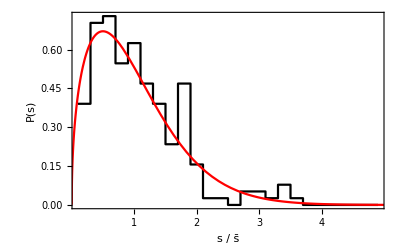

```mathematica
pall4=Show[phist4,pfit4,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

```mathematica
ρ4
```

6.83828

## We need to more closely examine the identical particle symmetries and any other symmetries in the Hamiltonian in order to understand these spectra.

We defined the Jacobi coordinates in the H-tree above so that:

(y⃗)^(12)=S_12 x⃗

where:

1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))

To keep things as general as possible I’ll assume for now that only particle 1 is of different mass and let m_2=m_3=m_4=m, and m_1=γ m  Then

μ_12=(γ m m)/(γ m+m)=mγ/(1+γ) ⟶ m/2

μ_34=m/2

μ_(12,34)=((γ m+m)(2m))/(3m+γ m)=2m(1+γ)/(3+γ)⟶ m

μ=((γ m m m m)/(γ m+3m))^(1/3)=(m(γ/(3+γ)))^(1/3) ⟶ (m/2^(2/3))

So for the equal-mass case:

2^(1/3)/(√m)(√(m/2) | -√(m/2) | 0 | 0
0 | 0 | √(m/2) | -√(m/2)
(√m)/2 | (√m)/2 | -(√m)/2 | -(√m)/2
m/(√(4m)) | m/(√(4m)) | m/(√(4m)) | m/(√(4m)))=2^(1/3)(√(1/2) | -√(1/2) | 0 | 0
0 | 0 | √(1/2) | -√(1/2)
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2)

and

x⃗=S_12^-1(y⃗)^(12)

Then

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)

Now note that we could use the same matrix S_12 to construct (y⃗)^(13) if the matrix were to act on a column vector (x_1
x_3
x_2
x_4)  instead of the usual vector x⃗= (x_1
x_2
x_3
x_4).  We can then say:

(x_1
x_3
x_2
x_4) =(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)=P_23 x⃗

Hence:

S_13=S_12 P_23

and

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)=S_12 P_23 S_12^-1(y⃗)^(12)

Similarly,

(y⃗)^(14)=S_14 x⃗=S_14 S_12^-1(y⃗)^(12)=S_12 P_24 S_12^-1(y⃗)^(12)

where

P_24=(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
S12=2^(1/3)({{√(1/2), -√(1/2), 0, 0}, {0, 0, √(1/2), -√(1/2)}, {1/2, 1/2, -1/2, -1/2}, {1/2, 1/2, 1/2, 1/2}});
```

```mathematica
P24=({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}});P23=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});P34=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});P14=({{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}});P13=({{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}});P12=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
𝒫12=Simplify[S12.P12.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫12]
```

(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
𝒫34=Simplify[S12.P34.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫34]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
𝒫14=Simplify[S12.P14.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫14]
```

(1/2 | -1/2 | -1/(√2)
-1/2 | 1/2 | -1/(√2)
-1/(√2) | -1/(√2) | 0)

```mathematica
𝒫13=Simplify[S12.P13.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫13]
```

(1/2 | 1/2 | -1/(√2)
1/2 | 1/2 | 1/(√2)
-1/(√2) | 1/(√2) | 0)

```mathematica
𝒫23=Simplify[S12.P23.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫23]
```

(1/2 | -1/2 | 1/(√2)
-1/2 | 1/2 | 1/(√2)
1/(√2) | 1/(√2) | 0)

```mathematica
𝒫24=Simplify[S12.P24.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫24]
```

(1/2 | 1/2 | 1/(√2)
1/2 | 1/2 | -1/(√2)
1/(√2) | -1/(√2) | 0)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14]]
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫24.𝒫13]]
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14.𝒫24.𝒫13]]
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

X_cm=(m_1 x_1+m_2 x_2+m_3 x_3+m_4 x_4)/(m_1+m_2+m_3+m_4)

ρ_1^(12)=x_1-x_2

ρ_2^(12)=x_3-x_4

ρ_3^(12)=(m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4)

and mass-scaled Jacobi coordinates as:

y_1^(12)=√(μ_12/μ)(x_1-x_2)

y_2^(12)=√(μ_34/μ)(x_3-x_4)

y_3^(12)=√((μ_(12,34))/μ)((m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4))

y_4^(12)=√(M/μ)X_cm

The convention here is that the superscript (12) indicates this coordinate system is convenient for treating the interaction between particles 1 and 2.  In matrix notation:

(y_1^(12)
y_2^(12)
y_3^(12)
y_4^(12))=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_2
x_3
x_4)

Now we define the hyperspherical coordinates as:

y_1^(12)=cos θ_12

y_2^(12)=sin θ_12 cos ϕ_12

y_3^(12)=sin θ_12 sin ϕ_12

```mathematica
Clear[μ4]
```

```mathematica
μ4=(μ12 μ34 μ1234)^(1/3)/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}
```

((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3)

```mathematica
A=1/(√μ4)({{√μ12, -√μ12, 0, 0}, {0, 0, √μ34, -√μ34}, {(√μ1234 m1)/(m1+m2), (√μ1234 m2)/(m1+m2), -(√μ1234 m3)/(m3+m4), -(√μ1234 m4)/(m3+m4)}, {m1/(√M), m2/(√M), m3/(√M), m4/(√M)}})/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}//FullSimplify
```

{{(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),0,0},{0,0,(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)},{(m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),(m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6))},{m1/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m2/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m3/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m4/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4))}}

Let’s just treat the equal mass case here...

```mathematica
({{x1}, {x2}, {x3}, {x4}})=FullSimplify[Inverse[A].({{x}, {y}, {z}, {XCM}})/.{m1->m,m2->m,m3->β m,m4->β m}];
```

```mathematica
Clear[R]
```

```mathematica
x12=Simplify[x1-x2];FullSimplify[x12,{m>0,β>0}]
x12hyp=Simplify[x12,m>0]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x12hyp,m>0]
```

(2^(1/3) x β^(1/3))/(1+β)^(1/6)

2^(1/3) R (β^2/(1+β))^(1/6) Cos[ϕ] Sin[θ]

```mathematica
x13=FullSimplify[x1-x3,{m>0,β>0}]
x13hyp=Simplify[x13]/.{x->R Sin[θ]Cos[ϕ],y-> R Sin[θ]Sin[ϕ],z-> R Cos[θ]};FullSimplify[x13hyp,{m>0,β>0}]
```

(√m x β-y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]-√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x14=FullSimplify[x1-x4,{m>0,β>0}]
x14hyp=Simplify[x14]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x14hyp,{m>0,β>0}]
```

(√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x23=Simplify[x2-x3,{m>0,β>0}]
x23hyp=Simplify[x23]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x23hyp,{m>0,β>0}]
```

-(√m x β+y √(m β)-z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]-Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x24=Simplify[x2-x4,{m>0,β>0}]
x24hyp=Simplify[x24]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x24hyp,{m>0,β>0}]
```

(-√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (-√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x34=Simplify[x3-x4,{m>0,β>0}]
x34hyp=Simplify[x3-x4,{m>0,β>0}]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x34hyp,{m>0,β>0}]
```

(2^(1/3) y)/(β (1+β))^(1/6)

(2^(1/3) R Sin[θ] Sin[ϕ])/(β (1+β))^(1/6)

```mathematica
Clear[unequalmassxij]
```

```mathematica
unequalmassxij[R_,β_]=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m->1,θ->t π,ϕ->f π}]
```

{2^(1/3) R (β^2/(1+β))^(1/6) Cos[f π] Sin[π t],(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]-√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-√β (√β Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(2^(1/3) R Sin[f π] Sin[π t])/((β+β^2)^(1/6))}

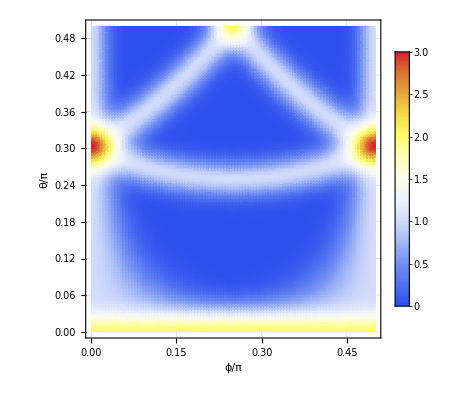

```mathematica
beta=1.0;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2],{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

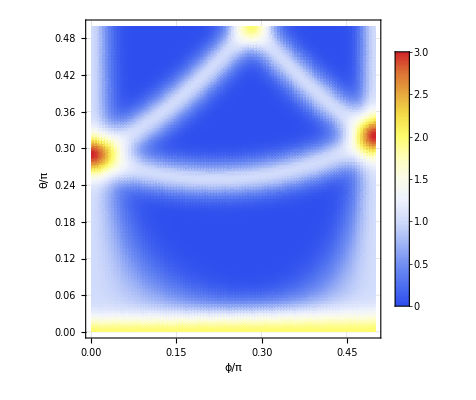

```mathematica
beta=1.5;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2]/.β->beta,{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

```mathematica
unequalmassxij[[1]]==0
```

5 2^(1/3) (β^2/(1+β))^(1/6) Cos[f π] Sin[π t]==0

```mathematica
c12[β_]:=ContourPlot[Evaluate[unequalmassxij[[1]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Black,FrameLabel->{"ϕ/π","θ/π"}]
c13[β_]:=ContourPlot[Evaluate[unequalmassxij[[2]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Red,FrameLabel->{"ϕ/π","θ/π"}];
c14[β_]:=ContourPlot[Evaluate[unequalmassxij[[3]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Blue,FrameLabel->{"ϕ/π","θ/π"}];
c23[β_]:=ContourPlot[Evaluate[unequalmassxij[[4]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Green,FrameLabel->{"ϕ/π","θ/π"}];
c24[β_]:=ContourPlot[Evaluate[unequalmassxij[[5]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Orange,FrameLabel->{"ϕ/π","θ/π"}];
c34[β_]:=ContourPlot[Evaluate[unequalmassxij[[6]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Yellow,FrameLabel->{"ϕ/π","θ/π"}];
```

```mathematica
c12[1.0]
```

-Graphics-

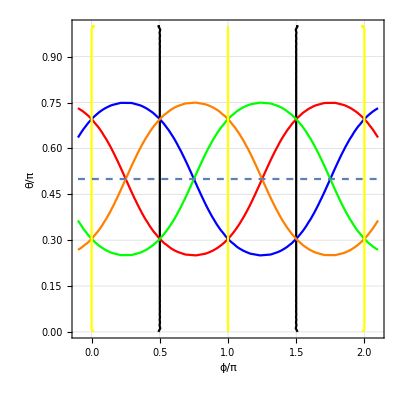

```mathematica
pall=Show[{c12,c13,c14,c23,c24,c34},Plot[0.5,{x,-.1,2.1},PlotStyle->Dashed]]
```

```mathematica
cptable=Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,0,.5},{t,0,.5},GridLines->Automatic,ContourStyle->Black],{i,1,6}];
```

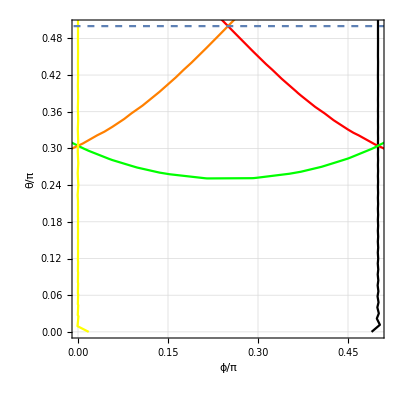

```mathematica
Show[pall,PlotRange->{{0,0.5},{0,0.5}}]
```